```mathematica
mins[simplex_,x_]:=Normalize[#-x]&/@simplex;
```

```mathematica
threeMinsQ[simplex_,x_]:=(Flatten[FirstPosition[#,Max[#]]&/@(mins[simplex,x].Transpose[simplex])]=={1,2,3});
```

```mathematica
newX[simplex_,x_]:=Module[{grid=mins[simplex,x],a},
a=Max/@(grid.Transpose[simplex]);
Rest[LinearSolve[Prepend[#,1]&/@grid,a]]
];
```

```mathematica
pointRunsAway[simplex_,x_]:=If[threeMinsQ[simplex,NestWhile[newX[simplex,#]&,x,threeMinsQ[simplex,#]&,1,10]],0,1];
```

```mathematica
iterationsToZero[simplex_,x_]:=With[{list=NestWhileList[newX[simplex,#]&,x,(Norm[#]>10^-9)&&(threeMinsQ[simplex,#])&,1,15]},
If[Norm[Last[list]]<=10^-9,Length[list],15]];
```

```mathematica
(*A=Normalize/@{{1,0},{-1,0.1},{-1,-0.1}};*)
A=Normalize/@{{1,0},{-1,0.3},{-1,-0.3}};
```

```mathematica
sample=Table[{-j/100.,i/100.},{i,-100,100},{j,-100,100}]
```

{{{1.,-1.},{0.99,-1.},{0.98,-1.},{0.97,-1.},{0.96,-1.},{0.95,-1.},{0.94,-1.},{0.93,-1.},{0.92,-1.},{0.91,-1.},{0.9,-1.},{0.89,-1.},{0.88,-1.},{0.87,-1.},{0.86,-1.},{0.85,-1.},{0.84,-1.},{0.83,-1.},165,{-0.83,-1.},{-0.84,-1.},{-0.85,-1.},{-0.86,-1.},{-0.87,-1.},{-0.88,-1.},{-0.89,-1.},{-0.9,-1.},{-0.91,-1.},{-0.92,-1.},{-0.93,-1.},{-0.94,-1.},{-0.95,-1.},{-0.96,-1.},{-0.97,-1.},{-0.98,-1.},{-0.99,-1.},{-1.,-1.}},199,{1}}
 |  |  |  |

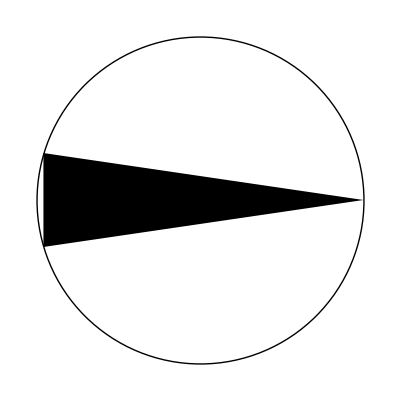

```mathematica
Graphics[{Circle[],Triangle[A]}]
```

```mathematica
ArrayPlot[Map[If[threeMinsQ[A,#],1,0]&,sample,{2}]]
```

-Graphics-

```mathematica
ArrayPlot[Map[pointRunsAway[A,#]&,sample,{2}]]
```

-Graphics-

```mathematica
ArrayPlot[Map[iterationsToZero[A,#]&,sample,{2}],PlotLegends->Automatic,ImageSize->Large]
```

-Graphics-

```mathematica
D[PiecewiseExpand[Abs[x],Reals],x]
```

Piecewise[{{-1, x<0}, {1, x>0}, {Indeterminate, True}}]